# The Lattice Boltzmann Method

Local velocity populations

#### Clear all symbols

```mathematica
ClearAll[populationArrows,populationPlot, filename,populationList, subList];
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

#### Create plot of local equilibrium distribution

```mathematica
ClearAll[directions,u,w0,feq,feq0,feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8];
```

```mathematica
u[ux_,uy_]:= √(ux^2+uy^2);

w0[rho_]:= (2 rho)/9;w1[rho_] := rho/18;w2[rho_]:=rho/36;
```

#### Rest distribution (zero velocity)

```mathematica
feq0[ux_,uy_] := w0(2-3 u[ux,uy]^2);
```

#### Horizontal/vertical direction

```mathematica
feq1[rho_,ux_,uy_] := w1[rho](2+6ux+9 ux^2-3 u[ux,uy]^2);
feq3[rho_,ux_,uy_] := w1[rho](2+6uy+9 uy^2-3 u[ux,uy]^2);
feq5[rho_,ux_,uy_] := w1[rho](2-6ux+9 ux^2-3 u[ux,uy]^2);
feq7[rho_,ux_,uy_] := w1[rho](2-6uy+9 uy^2-3 u[ux,uy]^2);
```

#### Diagonal directions

```mathematica
feq2[rho_,ux_,uy_] := w2[rho](1+3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq4[rho_,ux_,uy_] := w2[rho](1-3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
feq6[rho_,ux_,uy_] := w2[rho](1-3(ux+uy)+9ux uy + 3 u[ux,uy]^2);
feq8[rho_,ux_,uy_] := w2[rho](1+3(ux-uy)-9ux uy + 3 u[ux,uy]^2);
```

```mathematica
feq[rho_,ux_,uy_] :=Map[Apply[#,{rho,ux,uy}]&, {feq1,feq2,feq3,feq4,feq5,feq6,feq7,feq8}];
feq[2,0,0]
```

{2/9,1/18,2/9,1/18,2/9,1/18,2/9,1/18}

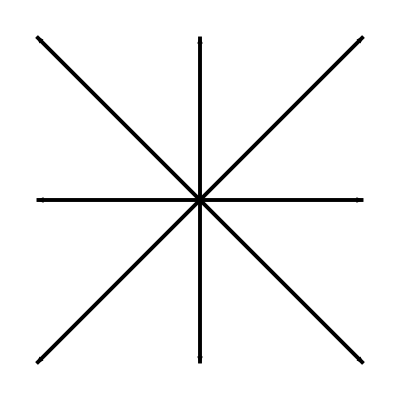

```mathematica
With[{scale=1},Graphics[{Thickness[0.007],Arrow[{{0,0}, 1.05*scale*#}]& /@{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}}}] ]
```

```mathematica
populationPlot[rho_,ux_,uy_]:=Module[{populations,scale,thickness,arrowCollor,directions,scaledDirections,populationScaledDirections,pArrows,pThickness,pCollor},
scale = 5;
thickness = 35;
arrowCollor = Red;
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
populations = feq[rho,ux,uy];
populationArrows[populations]
(*AppendTo[populations2,populations2[[1]]];
	f =Graphics[{EdgeForm[Dashed],Pink,Polygon[populations2]},AspectRatio->1,PlotRange->0.5]*)
];

Manipulate[populationPlot[rho,ux,uy],{{rho,2.5}, 0,5},{{ux,0},-√(1/12),√(1/12)},{{uy,0},-√(1/12),√(1/12)}]
```

```mathematica
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
(2+6(#[[1]]ux+#[[2]] uy)+9 ux^2-3 u[ux,uy]^2)&/@directions
```

{2+6 ux+9 ux^2-3 u[ux,uy]^2,2+9 ux^2+6 (ux+uy)-3 u[ux,uy]^2,2+9 ux^2+6 uy-3 u[ux,uy]^2,2+9 ux^2+6 (-ux+uy)-3 u[ux,uy]^2,2-6 ux+9 ux^2-3 u[ux,uy]^2,2+9 ux^2+6 (-ux-uy)-3 u[ux,uy]^2,2+9 ux^2-6 uy-3 u[ux,uy]^2,2+9 ux^2+6 (ux-uy)-3 u[ux,uy]^2}

Fluid flow: mesoscopic

#### Clear all symbols

```mathematica
ClearAll[populationArrows,populationPlot, filename,populationList, subList];
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

#### Create plot of velocity populations

```mathematica
populationArrows[populations_]:=Module[{scale2,thickness,arrowCollor,directions,scaledDirections,populationScaledDirections,pArrows,pThickness,pCollor},
scale2 = 1;
thickness = 35;
arrowCollor = Red;
directions = {{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}};
pArrows = (Arrow[{{0,0},(scale2*#)/If[Plus@@(#^2)>0,√(Plus@@(#^2)),1]}]&/@directions);
pThickness = AbsoluteThickness/@(thickness*populations);
pCollor = Table[arrowCollor,Length@directions];
Graphics@(Sequence@@{Transpose[{pCollor,pThickness,pArrows}],ImageSize->Tiny})

];
```

#### Get data from C++ simulation

```mathematica
SetDirectory[NotebookDirectory[]];
filename="population"<>".txt";
populationList = If[FileExistsQ[filename],Get[filename]];
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

#### Prepare data for presentation

```mathematica
subList = populationList[[All,2;;-2,2;;-2,;;-2]];
Map[populationArrows,subList,{3}][[1,2]]//MatrixForm;
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```

#### Presentation

```mathematica
ListAnimate[MatrixForm/@Map[populationArrows,subList,{3}],AnimationRunning->False]
SelectionMove[EvaluationNotebook[],Next, CellGroup];
FrontEndTokenExecute[EvaluationNotebook[],"Evaluate"];
```